# 计算物理范例

### 方程组的求解

```mathematica
Solve[x1+2x2+x3==0&&2x1+2x2+3x3==3&&-x1-3x2==0,{x1,x2,x3}]
```

{{x1→9,x2→-3,x3→-3}}

```mathematica
NSolve[x^2-10x+y^2+4==0&&x y^2+x-10y+4==0,{x,y},Reals]
```

{{x→2.25893,y→3.6724},{x→0.439871,y→0.453014}}

### 函数近似

InterpolatingFunction[…]

FittedModel[Sin[1.00025 x]]

Sin[1.00025 x]

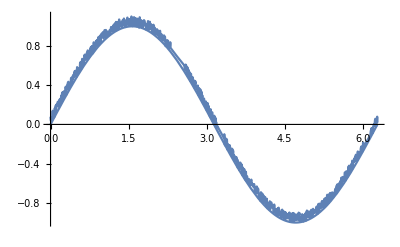

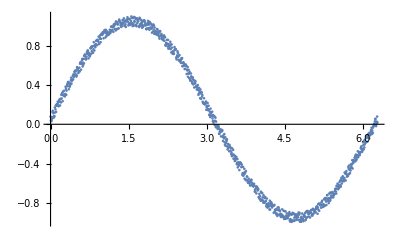

```mathematica
data = {Range[0,2Pi,2Pi/999],Sin[Range[0,2Pi,2Pi/999]]+RandomReal[{0,0.1},1000]};
interpf=Interpolation[Transpose[data]]
nol=NonlinearModelFit[Transpose[data],Sin[a*x],{a},{x}]
Normal[nol]
Show[Plot[interpf[x],{x,0,2Pi}],Plot[nol[x],{x,0,2Pi}]]
ListPlot[Transpose[data]]
```

### 导数的运算

```mathematica
f[x_,y_]:=(x^2+4 y^2-9)^2+(18y-14 x^2+45)^2
D[f[x,y],{{x,y}}]//Simplify
Series[1/(Cos[θ]-a),{θ,0,4}]
```

{4 x (-639+197 x^2-252 y+4 y^2),1620+504 y+64 y^3+8 x^2 (-63+2 y)}

1/(1-a)+θ^2/(2 (-1+a)^2)+((-5-a) θ^4)/(24 (-1+a)^3)+O[θ]^5

```mathematica
Integrate[Sin[x]*Cos[y],x,y]
```

-Cos[x] Sin[y]

```mathematica
Integrate[x^p(1-x)^q,{x,0,1},Reals]
```

ConditionalExpression[(ℝ Gamma[1+p] Gamma[1+q])/Gamma[2+p+q],Re[p]>-1&&Re[q]>-1]

### 求解微分方程(组）

```mathematica
DSolve[{y''[x]+9.8+0.01*y'[x]==0,y[0]==0,y[5]==40},y,x]
y'[x]/.%/.x->0
```

{{y→({x}↦-980. ⅇ^(-0.01 x) (1. ⅇ^(0.01 x) x-103.358 ⅇ^(0.01 x)+103.358))}}

{32.9058}

```mathematica
sol=NDSolve[{x''[t]==x[t]-y[t]-(3*x'[t])^2+(y'[t])^3+6*y''[t]+2t,y'''[t]==y''[t]-x'[t]+ⅇ^x[t]-t,x[1]==2,x'[1]==-4,y[1]==-2,y'[1]==7,y''[1]==6},{x,y},{t,1,1.6}]
Plot[{x[t]/.sol,y[t]/.sol},{t,1,1.6}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

```mathematica
DSolve[{u''[t]==-Pi^2(u[t]+1)/4,u[0]==0,u[1]==1},u,t]
```

{{u→Function[{t},-1+Cos[(π t)/2]+2 Sin[(π t)/2]]}}

### 求解偏微分方程

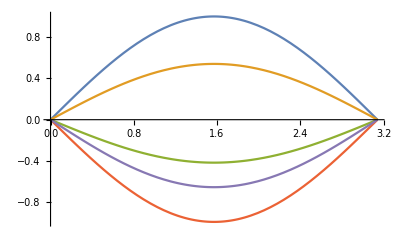
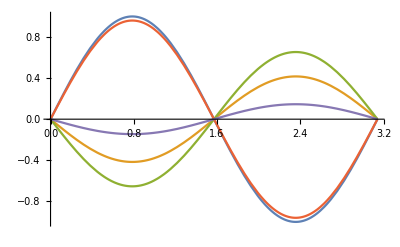
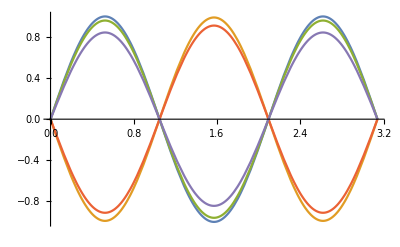
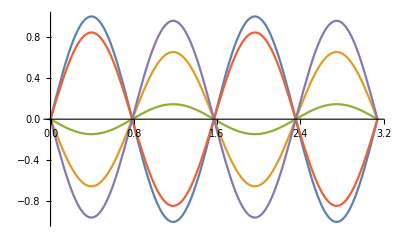

```mathematica
Block[{eqn,bc,ic,dsol,sol1},eqn = D[u[x, t], {t, 2}] == D[u[x, t], {x, 2}];bc={u[0,t]==0,u[π,t]==0};ic={u[x, 0] == Sin[m x], Derivative[0, 1][u][x, 0] == 0};dsol=DSolve[{eqn,bc,ic},u,{x,t},Assumptions->Element[m,Integers]];sol1[x_,t_]=u[x,t]/.dsol[[1]];Table[Show[Plot[Table[sol1[x,t],{t,0,4}]//Evaluate,{x,0,Pi},Ticks->False]],{m,4}]]
```

### 矩阵相关

#### 高斯消元的矩阵操作

```mathematica
(* 行列操作可以看作矩阵作用到另一个矩阵*)
Block[{M,A,Ap},M=IdentityMatrix[3];M[[1,2]]=λ;A=Table[a[i][j],{i,1,3},{j,1,3}];M.A//MatrixForm]
```

```mathematica
Block[{M,A,Ap},M=IdentityMatrix[3];M[[1,2]]=λ;A=Table[a[i][j],{i,1,3},{j,1,3}];A.M//MatrixForm]
```

```mathematica
(*选取合适的系数消去第一列其他元素*)
Block[{M1,M2,A,A1,A2,Ap},M1=IdentityMatrix[3];A=Table[a[i][j],{i,1,3},{j,1,3}];M1[[2,1]]=-A[[2,1]]/A[[1,1]];

M1[[3,1]]=-A[[3,1]]/A[[1,1]];
A1=M1.A;
M2=IdentityMatrix[3];
M2[[3,2]]=-A1[[3,2]]/A1[[2,2]];
A2=M2.A1;
Print["A1 = \n",A1//MatrixForm,"\n A2 = \n",A2//MatrixForm,"\n M2.M1 = \n",M2.M1//MatrixForm,"\n M2.M1.A = \n",M2.M1.A//Simplify//MatrixForm,"\n Invert M2.M1 = \n",Inverse[M2.M1]//MatrixForm]
]
```

A1 = 
(a[1][1] | a[1][2] | a[1][3]
0 | -(a[1][2] a[2][1])/(a[1][1])+a[2][2] | -(a[1][3] a[2][1])/(a[1][1])+a[2][3]
0 | -(a[1][2] a[3][1])/(a[1][1])+a[3][2] | -(a[1][3] a[3][1])/(a[1][1])+a[3][3])
 A2 = 
(a[1][1] | a[1][2] | a[1][3]
0 | -(a[1][2] a[2][1])/(a[1][1])+a[2][2] | -(a[1][3] a[2][1])/(a[1][1])+a[2][3]
0 | 0 | -(a[1][3] a[3][1])/(a[1][1])+((-(a[1][3] a[2][1])/(a[1][1])+a[2][3]) ((a[1][2] a[3][1])/(a[1][1])-a[3][2]))/(-(a[1][2] a[2][1])/(a[1][1])+a[2][2])+a[3][3])
 M2.M1 = 
(1 | 0 | 0
-(a[2][1])/(a[1][1]) | 1 | 0
-(a[3][1])/(a[1][1])-(a[2][1] ((a[1][2] a[3][1])/(a[1][1])-a[3][2]))/(a[1][1] (-(a[1][2] a[2][1])/(a[1][1])+a[2][2])) | ((a[1][2] a[3][1])/(a[1][1])-a[3][2])/(-(a[1][2] a[2][1])/(a[1][1])+a[2][2]) | 1)
 M2.M1.A = 
(a[1][1] | a[1][2] | a[1][3]
0 | -(a[1][2] a[2][1])/(a[1][1])+a[2][2] | -(a[1][3] a[2][1])/(a[1][1])+a[2][3]
0 | 0 | (a[1][3] (-a[2][2] a[3][1]+a[2][1] a[3][2])+a[1][2] (a[2][3] a[3][1]-a[2][1] a[3][3])+a[1][1] (-a[2][3] a[3][2]+a[2][2] a[3][3]))/(-a[1][2] a[2][1]+a[1][1] a[2][2]))
 Invert M2.M1 = 
(1 | 0 | 0
(a[2][1])/(a[1][1]) | 1 | 0
(a[3][1])/(a[1][1]) | -(a[1][2] a[3][1])/(a[1][1] (-(a[1][2] a[2][1])/(a[1][1])+a[2][2]))+(a[3][2])/(-(a[1][2] a[2][1])/(a[1][1])+a[2][2]) | 1)